-Graphics-

-Graphics-

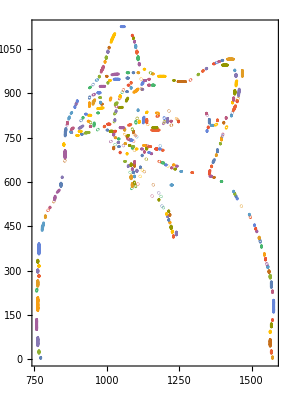

```mathematica
(*...This is the "Image curve" Mathematica Script...*)

param[x_,m_,t_]:=Module[{f,n=Length[x],nf},f=Chop[Fourier[x]][[;;Ceiling[Length[x]/2]]];
nf=Length[f];
Total[Rationalize[2 Abs[f]/Sqrt[n] Sin[Pi/2-Arg[f]+2. Pi Range[0,nf-1] t],.01][[;;Min[m,nf]]]]]

tocurve[Line[data_],m_,t_]:=param[#,m,t]&/@Transpose[data]

(*...This is where you copy the path to the file so Mathematica will pull the image...
..Make sure to do it for both the lines to get a view of a before, middle, after...*)

Import["C:\\Users\\miles\\Math 215\\cat iage.jpg"]
img=EdgeDetect[Import["C:\\Users\\miles\\Math 215\\cat iage.jpg"]]

img=Binarize[img~ColorConvert~"Grayscale"~ImageResize~1000~Blur~1]~Blur~1;
lines=Cases[Normal@ListContourPlot[Reverse@ImageData[img],Contours->{1}],_Line,-1];

ParametricPlot[Evaluate[tocurve[#,20,t]&/@lines],{t,0,1},Frame->True,Axes->False]
```

```mathematica
(*...This is the "Person curve" of Brother Woodruff...*)
Block[{$IterationLimit=Infinity},f[10^9]]

param[x_,m_,t_]:=Module[{f,n=Length[x],nf},f=Chop[Fourier[x]][[;;Ceiling[Length[x]/2]]];
nf=Length[f];
Total[Rationalize[2 Abs[f]/Sqrt[n] Sin[Pi/2-Arg[f]+2. Pi Range[0,nf-1] t],.01][[;;Min[m,nf]]]]]

tocurve[Line[data_],m_,t_]:=param[#,m,t]&/@Transpose[data]

(*...This is where you copy the path to the file so Mathematica will pull the image...
..Make sure to do it for both the lines to get a view of a before, middle, after...*)

Import["C:\\Users\\miles\\Pictures\\woodruff.png"]
img=EdgeDetect[Import["C:\\Users\\miles\\Pictures\\woodruff.png"],6]

img=Binarize[img~ColorConvert~"Grayscale"~ImageResize~600~Blur~1]~Blur~1;
lines=Cases[Normal@ListContourPlot[Reverse@ImageData[img],Contours->{1}],_Line,-1];

ParametricPlot[Evaluate[tocurve[#,20,t]&/@lines],{t,0,1},Frame->True,Axes->False]
```

f[1000000000]

-Graphics-

-Graphics-

-Graphics-